# Sveral plots for a Bessel pressure field

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/antonio/Dropbox/_Papers/[Matheus] Paper 1/Figuras paper

## Beam coefficients

```mathematica
Gbes[l_,m_,β_,o_]=ⅈ^(l-m)Sqrt[(2l+1) 4π]Sqrt[((l-m)!)/((l+m)!)]LegendreP[l,m,Cos[β]]KroneckerDelta[o,m];
```

## Medium parameters

```mathematica
ρI= 997; (*agua*)
ρE= 1275/1000;(*ar*)
cI=1482;(*agua*)
cE=34087/100;(*ar*)
α =(ρI cI)/(ρE cE);
z=0;
NMax=15;
β=π/4;
```

```mathematica
f=40000;
```

## Onda Bessel

Simplification for LegendreP with θ=π/2

```mathematica
ll=RandomInteger[{0,10}]
mm=RandomInteger[{-ll,ll}]
LegendreP[ll,mm,0]
Piecewise[{{ⅈ^(ll+mm)((ll+mm-1)!!/(ll-mm)!!),And[EvenQ[ll+mm],mm≥0]},{(-1)^mm  ⅈ^(ll-mm)((ll-mm-1)!!/(ll+mm)!!)((ll+mm)!/(ll-mm)!),And[EvenQ[ll+mm],mm<0]}}]
Clear[ll,mm]
```

9

3

3465/16

3465/16

```mathematica
kr=13;
pontos=40;
samplePoints=6500;
```

```mathematica
GridXY=N[RandomSample[Union[DeleteCases[Flatten[ParallelTable[{x,y},{x,-kr,kr,kr/pontos},{y,-kr,kr,kr/pontos}],1],{0,0}],DeleteCases[Flatten[ParallelTable[{x,y},{x,-2,2,2/11},{y,-2,2,2/11}],1],{0,0}]],samplePoints]];
```

```mathematica
PincBes[r_,ϕ_,o_]:=Sum[SphericalBesselJ[l,2π f /cE r](Sqrt[(2l+1)/(4π)((l-m)!)/((l+m)!)](Piecewise[{{ⅈ^(l+m)((l+m-1)!!/(l-m)!!),And[EvenQ[l+m],m≥0]},{(-1)^m  ⅈ^(l-m)((l-m-1)!!/(l+m)!!)((l+m)!/(l-m)!),And[EvenQ[l+m],m<0]}}] Exp[ⅈ m ϕ])) Gbes[l,m,β,o],{l,0,NMax},{m,-l,l}];
```

```mathematica
BesselZeroReconst=ParallelMap[{#[[1]],#[[2]],N[Abs[PincBes[Sqrt[#[[1]]^2+#[[2]]^2]/(2π f/cE),ArcTan[#[[1]],#[[2]]],0]]]}&,GridXY];
```

```mathematica
BesselTwoReconst=ParallelMap[{#[[1]],#[[2]],N[Abs[PincBes[Sqrt[#[[1]]^2+#[[2]]^2]/(2π f/cE),ArcTan[#[[1]],#[[2]]],2]]]}&,GridXY];
```

```mathematica
Speak["This program is complet.  Please run next task"]
```

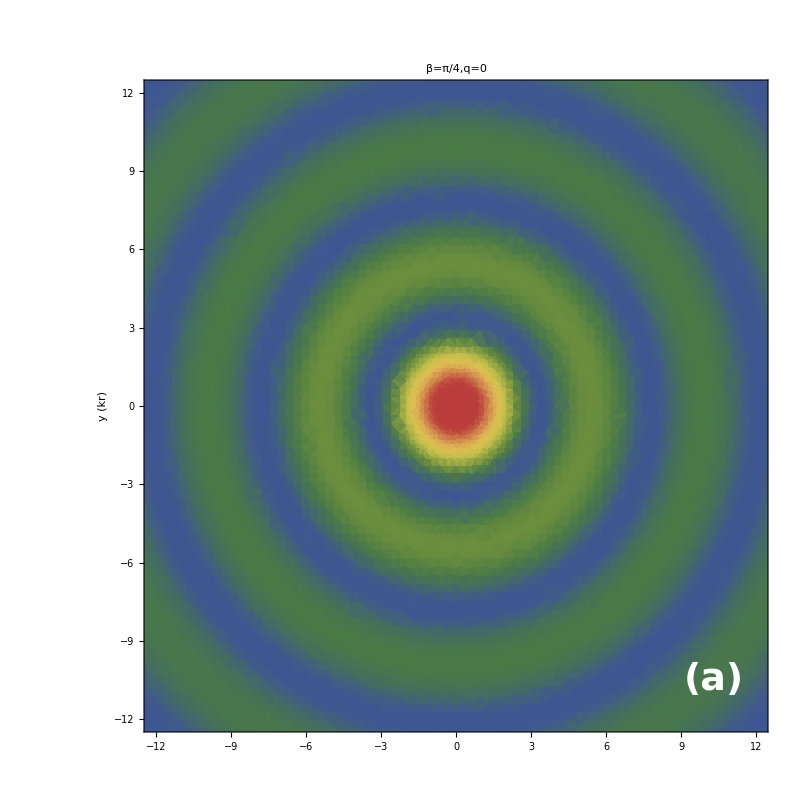

```mathematica
figura1=Show[ListDensityPlot[BesselZeroReconst,PlotRange->{{-12,12},{-12,12},All},ImageSize->800,PlotLegends->None,PlotLabel->Style["β=π/4,q=0",32],Frame->True,LabelStyle->Directive[Black,FontSize->32,FontFamily->"Helvetica"],FrameStyle->Directive[Black,FontSize->32,FontFamily->"Helvetica"],ColorFunction->"DarkRainbow",InterpolationOrder->2,PerformanceGoal->"Quality",PlotTheme->"Detailed",PlotRangePadding->None,ColorFunctionScaling->True,FrameLabel->{{"y (kr)",None},{None,None}},ImageMargins->0,ImageSize->800],Graphics[Text[Style["(a)",FontFamily->"Helvetica",White,Bold,38],{11.5,-10.5},{1,0}]]]
```

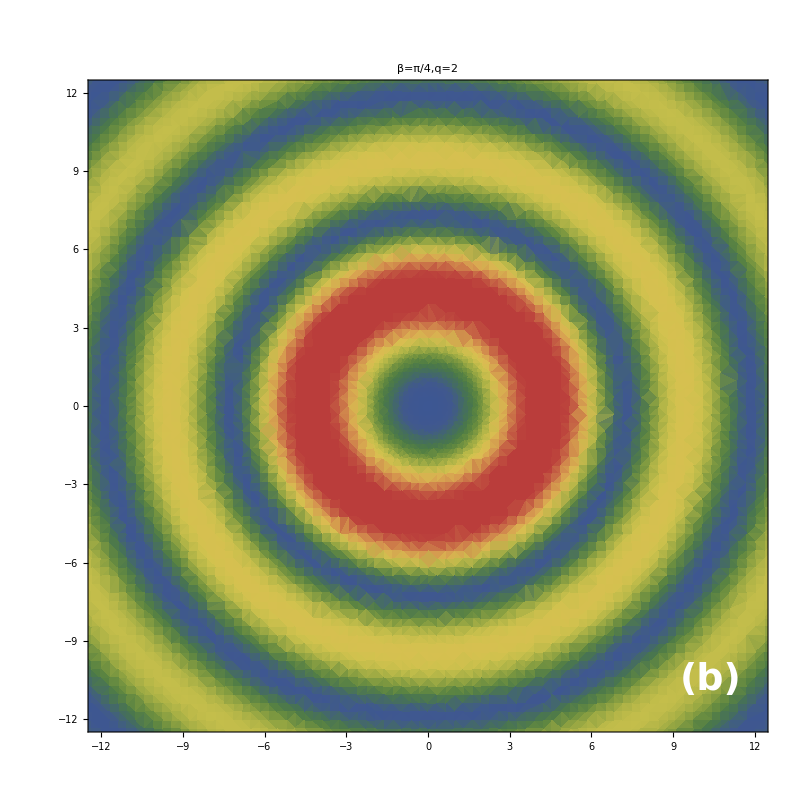

```mathematica
figura2=Show[ListDensityPlot[BesselTwoReconst,PlotRange->{{-12,12},{-12,12},All},ImageSize->800,PlotLegends->None,PlotLabel->Style["β=π/4,q=2",32],Frame->True,LabelStyle->Directive[Black,FontSize->32,FontFamily->"Helvetica"],FrameStyle->Directive[Black,FontSize->32,FontFamily->"Helvetica"],ColorFunction->"DarkRainbow",InterpolationOrder->2,PerformanceGoal->"Quality",PlotTheme->"Detailed",PlotRangePadding->None,ColorFunctionScaling->True,FrameLabel->{{"",None},{None,None}},ImageMargins->0,ImageSize->800],Graphics[Text[Style["(b)",FontFamily->"Helvetica",White,Bold,38],{11.5,-10.5},{1,0}]]]
```

```mathematica
ordem=0;
figura3=Show[DensityPlot[N[Abs[BesselJ[ordem,Sqrt[x^2+y^2] Sin[β]]Exp[ⅈ ordem ArcTan[x,y]]]],{x,-(kr-1),(kr-1)},{y,-(kr-1),(kr-1)},PlotRange->{{-12,12},{-12,12},All},ImageSize->800,PlotLegends->None,Frame->True,LabelStyle->Directive[Black,FontSize->32,FontFamily->"Helvetica"],FrameStyle->Directive[Black,FontSize->32,FontFamily->"Helvetica"],ColorFunction->"DarkRainbow",PerformanceGoal->"Quality",PlotTheme->"Detailed",PlotRangePadding->None,ColorFunctionScaling->True,FrameLabel->{{"y (kr)",None},{"x (kr)",None}},PlotPoints->150,ImageMargins->0],Graphics[Text[Style["(c)",FontFamily->"Helvetica",White,Bold,38],{11.5,-10.5},{1,0}]]]
```

-Graphics-

```mathematica
ordem=2;
figura4=Show[DensityPlot[N[Abs[BesselJ[ordem,Sqrt[x^2+y^2] Sin[β]]Exp[ⅈ ordem ArcTan[x,y]]]],{x,-(kr-1),(kr-1)},{y,-(kr-1),(kr-1)},PlotRange->{{-12,12},{-12,12},All},ImageSize->800,PlotLegends->None,Frame->True,LabelStyle->Directive[Black,FontSize->32,FontFamily->"Helvetica"],FrameStyle->Directive[Black,FontSize->32,FontFamily->"Helvetica"],ColorFunction->"DarkRainbow",PerformanceGoal->"Quality",PlotTheme->"Detailed",PlotRangePadding->None,ColorFunctionScaling->True,FrameLabel->{{"",None},{"x (kr)",None}},PlotPoints->150,Exclusions->None,ImageMargins->0],Graphics[Text[Style["(d)",FontFamily->"Helvetica",White,Bold,38],{11.5,-10.5},{1,0}]]]
```

-Graphics-

```mathematica
bl=BarLegend["DarkRainbow",LegendMarkerSize->{40,1000},Ticks->None];
```

```mathematica
nbl=RawBoxes@Replace[ToBoxes[bl],Rule[FrameTicks,_]:>Rule[FrameTicks,False],∞];
```

```mathematica
AllFig=Legended[GraphicsGrid[{{figura1,figura2},{figura3,figura4}},ImageSize->1200,Frame->None,Spacings->{-40, -5}],Placed[nbl,Right]]
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/antonio/Dropbox/_Papers/[Matheus] Paper 1/Figuras paper

```mathematica
Export["BesselReconstru.tiff",AllFig,ImageSize->1200,ImageResolution->500,"ImageEncoding"->"LZW"]
```

BesselReconstru.tiff

```mathematica
Export["BesselReconstru2.png",AllFig,ImageSize->1200,ImageResolution->300]
```

BesselReconstru2.png